# Correlation and Regression

## Theme

```mathematica
fontLabels=Directive[FontFamily->"Libertinus Serif",FontSize->22];
fontTicks=Directive[FontFamily->"Libertinus Serif",FontSize->18];

(* https://mathematica.stackexchange.com/questions/54545/is-it-possible-to-define-a-new-plottheme *)
Begin["System`PlotThemeDump`"];
Themes`ThemeRules;(*preload Theme system*)

resolvePlotTheme["myThemeBasic",def:_String]:=Themes`SetWeight[
Join[
{ImageSize->Large},
{LabelStyle->fontLabels},
{TicksStyle->fontTicks},
{FrameTicksStyle->fontTicks},
(* 102 is the default grey level of Mathematica *)
{AxesStyle->Directive[AbsoluteThickness[0.3],GrayLevel[102/255]]}
]
,$ComponentWeight];
resolvePlotTheme["myTheme",def:_String]:=Themes`SetWeight[
Join[
resolvePlotTheme["myThemeBasic",def],
{PlotStyle->Directive[PointSize[0.013],Thick]}
]
,$ComponentWeight];
resolvePlotTheme["myThemeBW",def:_String]:=Themes`SetWeight[
Join[
resolvePlotTheme["myTheme",def],
{PlotStyle->Thread@Directive[{GrayLevel[0.2],GrayLevel[0.8]},Thick,{Automatic,Dashed}]}
]
,$ComponentWeight];
(* Do not adjust point sizes for region plots *)
resolvePlotTheme["myTheme",def:"RegionPlot"]:=Themes`SetWeight[
Join[
resolvePlotTheme["myThemeBasic",def],
{PlotStyle->Automatic}
]
,$ComponentWeight];

End[];

it[var_]:=Style[var,FontSlant->Italic]
bf[var_]:=Style[var,FontWeight->Bold]
bi[var_]:=bf[it[var]]
```

## Part 1: Sign?

The sign of s_XY,r_XY and m_(Y,X) share all the same properties since the only difference between them is the different scaling via the standard deviations and they are always positive.

## Part 2: Check the Slope Equation

```mathematica
data={{2,20},{2,18},{3,32},{5,40},{8,60}};
data//MatrixForm
```

(2 | 20
2 | 18
3 | 32
5 | 40
8 | 60)

```mathematica
{Subscript[μ, x],Subscript[μ, y]}=Mean[data]
```

{4,34}

```mathematica
lm=LinearModelFit[data,x,x]
```

FittedModel[7.53846+6.61538 x]

```mathematica
slope=lm["BestFitParameters"][[2]]
```

6.61538

```mathematica
{Subscript[σ, x],Subscript[σ, y]}=StandardDeviation[data]//N
```

{2.54951,17.088}

```mathematica
slope*Subscript[σ, x]/Subscript[σ, y]
```

0.987007

```mathematica
Correlation[data]//N//MatrixForm
```

(1. | 0.987007
0.987007 | 1.)

The result is indeed the same.

## Part 3: Slope

A higher value for the correlation coefficient does not necessarily indicate that the slope of the regression line is higher (it is only a measure of how strong the linear relationship is, not how this linear relationship looks like). The thing is that when the slope of the line changes, the standard deviations usually changes as well. E.g. if we increase the slope of the line, s_Y might increase and s_X decrease, so s_X/s_Ygets smaller and hence acts as an opposing force.

## Part 4: Exact Linear Relationship

When the points are moved vertically to the line, s_Y decreases since the points mover closer to the mean. When all points are exactly located on the line, we cannot decrease s_Y further. Note: the same argument may also be true for s_X but this is a bit trickier since then also the slope of the regression line changes. This is not true for s_Y since the regression line uses the (quadratic) distance between the points and the line.

In the case of exact linear relationship, the relation s_X/s_Y is exactly the inverse slope, i.e. m^-1.

## Part 5: Correlation and Causality

The correlation coefficient says nothing about causality, i.e. whether more police really is the cause of the increase crime (as indicated). Usually, there are two main reasons why the relationship indicated by r_XY might not be true.

Influence of different variables: there might be another variable which influences X and Y and hence results in a high correlation. Here, maybe there is an event where a lot of people attend so that we naturally need more police and we have naturally more crimes (probably not the case here, more likely is the next point).

Backwards causality: it might be that not X influences Y but the other way around. Here, this would mean that due to higher crime rates we need more police (this is definately a problem here).

## Code

```mathematica
deviationBar[y0_,μ_,σ_,reverse_?BooleanQ,scale_]:=Block[{midBar,textStyle,lineStyle,rev},
midBar=scale;
textStyle=CurrentValue[{StyleDefinitions,"GraphicsLabel"}];
rev=Piecewise[{{Reverse, reverse}, {Identity, True}}];

Graphics[{
{
RGBColor[0.880722, 0.611041, 0.142051],
Thickness[Absolute[1.6]],
Line[{rev[{μ-σ,+y0}],rev[{μ+σ,+y0}]}],
Line[{rev[{μ,midBar+y0}],rev[{μ,-midBar+y0}]}],
Line[{rev[{μ-σ,midBar+y0}],rev[{μ-σ,-midBar+y0}]}],
Line[{rev[{μ+σ,midBar+y0}],rev[{μ+σ,-midBar+y0}]}]
},

Text[Style["μ",FontFamily->"Libertinus Serif",FontSize->16,textStyle],rev[{μ,-2.3*midBar+y0}]],
Text[Style["-σ",FontFamily->"Libertinus Serif",FontSize->16,textStyle],rev[{μ-0.5*σ,-2.3*midBar+y0}]],
Text[Style["+σ",FontFamily->"Libertinus Serif",FontSize->16,textStyle],rev[{μ+0.5*σ,-2.3*midBar+y0}]]
}]
]
```

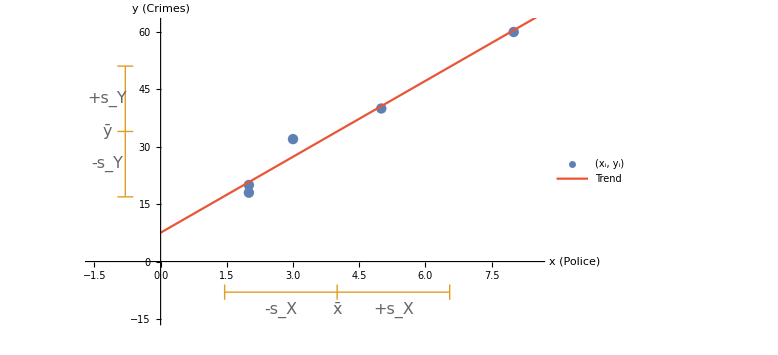

```mathematica
Show[
ListPlot[data,
PlotTheme->"myTheme",
AxesLabel->{
Row[{Style["x",FontSlant->Italic]," (Police)"}],
Row[{Style["y",FontSlant->Italic]," (Crimes)"}]
},
PlotLegends->{"(x_i, y_i)"},
PlotRange->{{-1.5,8.5},{-15,62}}
],
Plot[lm[x],{x,0,10},PlotTheme->"myTheme",PlotStyle->RGBColor[0.915, 0.3325, 0.2125],PlotLegends->{"Trend"}],

deviationBar[-8,Subscript[μ, x],Subscript[σ, x],False,2]/.{"μ"->"x̄","-σ"->"-s_X","+σ"->"+s_X"},
deviationBar[-0.8,Subscript[μ, y],Subscript[σ, y],True,0.18]/.{"μ"->"ȳ","-σ"->"-s_Y","+σ"->"+s_Y"}
]
```